## Importing and definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]]
```

```mathematica
ClearAll[ParityMatrix];ParityMatrix[L_]:=Normal@SparseArray[{FromDigits[#,2]+1,FromDigits[Reverse[#],2]+1}->1.&/@Tuples[{0,1},L]]
```

```mathematica
PlotPr[rTilde_]:=Show[Histogram[rTilde,Automatic,"PDF",PlotRange->{{0.,1.},{-0.01,2.01}},Frame->True,FrameStyle->Directive[Black,FontSize->20],FrameLabel->{HoldForm[r̃], HoldForm[P[r̃]]},ImageSize->400],Plot[27/4*(r+r^2)/((1+r+r^2)^(5/2)),{r,0,1},PlotStyle->Directive[Blue,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],
Plot[2/(1+r)^2,{r,0,1},PlotStyle->Directive[Red,Thickness[0.015],Dashing[0.03],Opacity[0.75]]],
(*The legends in the Epilog are starting here*)Epilog->Inset[LineLegend[{Directive[Red,Thickness[0.015],Dashing[0.03]],Directive[Blue,Thickness[0.015],Dashing[0.03]]},{"Poisson","GOE"},LabelStyle->Directive[Black,FontSize->20],
LegendLayout->"Row", (*Reduce vertical spacing*)
LegendMarkerSize->{40,5} (*Adjusts marker size to reduce spacing*)
],Scaled[{0.61,0.87}]]
(*End of the Legends*)]
```

### Mejora de Parity

Cómo funciona la función actual

```mathematica
Parity[{0,0,1,0},2]
```

{0,1,0,0}

Esto se puede precomputar:

```mathematica
L=4;FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]
```

{1,9,5,13,3,11,7,15,2,10,6,14,4,12,8,16}

La mejora sería lo siguiente:

```mathematica
L=4;reorderedIndices=FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L](*precomputar esta lista*);
ψ[[reorderedIndices]]
```

## Parity

```mathematica
L=2;{FromDigits[#,2]+1,FromDigits[Reverse[#],2]+1}&/@Tuples[{0,1},L]
```

{{1,1},{2,3},{3,2},{4,4}}

```mathematica
Select[Tuples[{0,1},L],PalindromeQ]
```

{{0,0,0},{0,1,0},{1,0,1},{1,1,1}}

```mathematica
(*base*)
base=DeleteDuplicatesBy[Tuples[{0,1},3],First[Sort[{#,Reverse[#]}]]&]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,1},{1,1,1}}

hz

```mathematica
(*diagonal*)
hz=If[PalindromeQ[#],1,1/2]*Total[(-1)^#]&/@base
```

{3,1/2,1,-1/2,-1,-3}

```mathematica
#.(Pauli[{3,0,0}]+Pauli[{0,3,0}]+Pauli[{0,0,3}]).#&[{1,0,0,0,0,0,0,0}]
```

3

```mathematica
FromDigits[{0,1,0},2]
```

2

J

```mathematica
(*diagonal*)
J=Total[(-1)^Differences[#]]&/@base
```

{2,0,-2,0,-2,2}

```mathematica
(Pauli[{3,3,0}]+Pauli[{0,3,3}]).{1,0,0,0,0,0,0,0}
(Pauli[{3,3,0}]+Pauli[{0,3,3}]).{0,0,1,0,0,0,0,0}
(Pauli[{3,3,0}]+Pauli[{0,3,3}]).{0,0,0,1/√2,0,0,1/√2,0}
```

{2,0,0,0,0,0,0,0}

{0,0,-2,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

hx

```mathematica
pos=Flatten[Position[base,Reverse[Mod[ConstantArray[1,L]+#,2]]]&/@base]
```

{6,4,5,2,3,1}

```mathematica
Mod[ConstantArray[1,L]+#,2]&/@base
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,0},{0,0,0}}

```mathematica
A=SparseArray[Transpose[{pos,Range[Length[base]]}]->1]
```

SparseArray[…]

```mathematica
A+DiagonalMatrix[-J+hz]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 1
0 | 1/2 | 0 | 1 | 0 | 0
0 | 0 | 3 | 0 | 1 | 0
0 | 1 | 0 | -1/2 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | -5)

```mathematica
{{0,1,0},Mod[{0,1,0}+#,2]}&/@IdentityMatrix[3]
```

{{{0,1,0},{1,1,0}},{{0,1,0},{0,0,0}},{{0,1,0},{0,1,1}}}

```mathematica
?IsingNNOpenHamiltonian
```

```mathematica
IsingNNOpenHamiltonian[1,1,1,L]//MatrixForm
```

(1. | 1. | 1. | 0. | 1. | 0. | 0. | 0.
1. | 1. | 0. | 1. | 0. | 1. | 0. | 0.
1. | 0. | 3. | 1. | 0. | 0. | 1. | 0.
0. | 1. | 1. | -1. | 0. | 0. | 0. | 1.
1. | 0. | 0. | 0. | 1. | 1. | 1. | 0.
0. | 1. | 0. | 0. | 1. | 1. | 0. | 1.
0. | 0. | 1. | 0. | 1. | 0. | -1. | 1.
0. | 0. | 0. | 1. | 0. | 1. | 1. | -5.)

```mathematica
newIndices=FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L](*indices*);
eigenvals={};

(* Construir Hamiltoniano y diagonalizarlo *)
H=IsingNNOpenHamiltonian[(*hx*)1.,1,1,(*L*)3];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];

(* Encontrar la posición de los eigenvectores pares *)
eigenvecsParities=Round[Map[Braket[#,#[[newIndices]]]&,eigVecs],10.^0];
evenEigenvecsPositions=Flatten[Position[eigenvecsParities,1.]];
EvenEigVals=eigVals[[evenEigenvecsPositions]]//Sort
```

{-5.65388,-1.69216,-0.399465,0.946864,2.691,4.10764}

```mathematica
evenBasis=Normalize[SparseArray[Thread[{FromDigits[#,2],FromDigits[Reverse[#],2]}+1->1],2^L]]&/@base//Normal
```

{{1,0,0,0,0,0,0,0},{0,1/(√2),0,0,1/(√2),0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1/(√2),0,0,1/(√2),0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1}}

```mathematica
Table[Braket[i,H.j],{i,evenBasis},{j,evenBasis}]//Eigenvalues//Sort
```

{-5.65388,-1.69216,-0.399465,0.946864,2.691,4.10764}

## Ising

## Global parameters

```mathematica
(*Subscript[h, x]: magnetic field in x direction. L: number of spins*)
{hx,L}={1.,11}
```

{1.,11}

## Mean level spacing ratio (r_n)(h_z/h_x,J/h_x)

### Single

```mathematica
SortBy[Select[MeanLevelSpacingRatioData,#[[1]]==0.01&],#[[2]]&]
```

{{0.01,0.01,0.353427},{0.01,0.02,0.379699},{0.01,0.03,0.406734},{0.01,0.04,0.429054},{0.01,0.06,0.426594},{0.01,0.07,0.422336},{0.01,0.08,0.420608},{0.01,0.09,0.448161},{0.01,0.11,0.408424},{0.01,0.12,0.443104},{0.01,0.13,0.422237},{0.01,0.14,0.387188},{0.01,0.16,0.373297},{0.01,0.17,0.376144},{0.01,0.18,0.330376},{0.01,0.19,0.371827},{0.01,0.21,0.42232},{0.01,0.22,0.408056},{0.01,0.23,0.357279},{0.01,0.24,0.366624},{0.01,0.26,0.427637},{0.01,0.27,0.406158},{0.01,0.28,0.459745},{0.01,0.29,0.436054},{0.01,0.31,0.355395},{0.01,0.32,0.282751},{0.01,0.33,0.386485},{0.01,0.34,0.407647},{0.01,0.36,0.390472},{0.01,0.37,0.357766},{0.01,0.38,0.413055},{0.01,0.39,0.397963},{0.01,0.41,0.42481},{0.01,0.42,0.405814},{0.01,0.43,0.406325},{0.01,0.44,0.449284},{0.01,0.46,0.362063},{0.01,0.47,0.407136},{0.01,0.48,0.385663},{0.01,0.49,0.398059},{0.01,0.51,0.35294},{0.01,0.52,0.386477},{0.01,0.53,0.352562},{0.01,0.54,0.410176},{0.01,0.56,0.450542},{0.01,0.57,0.387153},{0.01,0.58,0.433471},{0.01,0.59,0.446705},{0.01,0.61,0.398805},{0.01,0.62,0.449026},{0.01,0.63,0.394545},{0.01,0.64,0.42016},{0.01,0.66,0.347699},{0.01,0.67,0.415167},{0.01,0.68,0.439781},{0.01,0.69,0.396467},{0.01,0.71,0.397382},{0.01,0.72,0.364233},{0.01,0.73,0.411983},{0.01,0.74,0.408981},{0.01,0.76,0.374921},{0.01,0.77,0.423724},{0.01,0.78,0.425647},{0.01,0.79,0.443047},{0.01,0.81,0.381842},{0.01,0.82,0.460368},{0.01,0.83,0.452965},{0.01,0.84,0.398808},{0.01,0.86,0.393456},{0.01,0.87,0.445932},{0.01,0.88,0.442853},{0.01,0.89,0.462706},{0.01,0.91,0.452167},{0.01,0.92,0.441358},{0.01,0.93,0.41308},{0.01,0.94,0.408182},{0.01,0.96,0.453472},{0.01,0.97,0.459103},{0.01,0.98,0.370808},{0.01,0.99,0.465527},{0.01,1.01,0.398937},{0.01,1.02,0.430442},{0.01,1.03,0.429925},{0.01,1.04,0.417496},{0.01,1.06,0.376606},{0.01,1.07,0.434552},{0.01,1.08,0.394154},{0.01,1.09,0.37567},{0.01,1.11,0.410654},{0.01,1.12,0.393684},{0.01,1.13,0.381475},{0.01,1.14,0.410263},{0.01,1.16,0.444343},{0.01,1.17,0.42777},{0.01,1.18,0.430791},{0.01,1.19,0.434664},{0.01,1.21,0.405357},{0.01,1.22,0.436152},{0.01,1.23,0.443049},{0.01,1.24,0.435725},{0.01,1.26,0.398437},{0.01,1.27,0.422505},{0.01,1.28,0.389036},{0.01,1.29,0.392906},{0.01,1.31,0.431983},{0.01,1.32,0.456923},{0.01,1.33,0.408849},{0.01,1.34,0.396315},{0.01,1.36,0.43102},{0.01,1.37,0.451554},{0.01,1.38,0.452668},{0.01,1.39,0.423765},{0.01,1.41,0.413793},{0.01,1.42,0.442183},{0.01,1.43,0.457477},{0.01,1.44,0.427128},{0.01,1.46,0.398149},{0.01,1.47,0.394468},{0.01,1.48,0.387938},{0.01,1.49,0.418586},{0.01,1.51,0.404809},{0.01,1.52,0.421626},{0.01,1.53,0.429028},{0.01,1.54,0.415996},{0.01,1.56,0.389293},{0.01,1.57,0.415106},{0.01,1.58,0.376251},{0.01,1.59,0.426372},{0.01,1.61,0.389281},{0.01,1.62,0.385157},{0.01,1.63,0.387989},{0.01,1.64,0.407713},{0.01,1.66,0.4051},{0.01,1.67,0.389866},{0.01,1.68,0.419745},{0.01,1.69,0.407673},{0.01,1.71,0.40706},{0.01,1.72,0.428094},{0.01,1.73,0.432513},{0.01,1.74,0.411114},{0.01,1.76,0.398101},{0.01,1.77,0.407724},{0.01,1.78,0.441834},{0.01,1.79,0.391533},{0.01,1.81,0.367428},{0.01,1.82,0.413771},{0.01,1.83,0.39887},{0.01,1.84,0.417493},{0.01,1.86,0.435077},{0.01,1.87,0.413912},{0.01,1.88,0.424366},{0.01,1.89,0.416665},{0.01,1.91,0.381597},{0.01,1.92,0.394073},{0.01,1.93,0.409308},{0.01,1.94,0.403016},{0.01,1.96,0.427299},{0.01,1.97,0.454393},{0.01,1.98,0.413856},{0.01,1.99,0.395643},{0.01,2.01,0.435834},{0.01,2.02,0.403785},{0.01,2.03,0.421308},{0.01,2.04,0.44001},{0.01,2.06,0.402058},{0.01,2.07,0.409373},{0.01,2.08,0.416699},{0.01,2.09,0.370891},{0.01,2.11,0.384031},{0.01,2.12,0.404135},{0.01,2.13,0.400962},{0.01,2.14,0.389998},{0.01,2.16,0.414703},{0.01,2.17,0.445806},{0.01,2.18,0.418566},{0.01,2.19,0.411836},{0.01,2.21,0.384629},{0.01,2.22,0.412741},{0.01,2.23,0.385835},{0.01,2.24,0.428333},{0.01,2.26,0.43278},{0.01,2.27,0.374849},{0.01,2.28,0.425984},{0.01,2.29,0.42712},{0.01,2.31,0.445611},{0.01,2.32,0.431161},{0.01,2.33,0.424553},{0.01,2.34,0.427638},{0.01,2.36,0.434833},{0.01,2.37,0.414935},{0.01,2.38,0.46106},{0.01,2.39,0.398956},{0.01,2.41,0.407952},{0.01,2.42,0.398702},{0.01,2.43,0.397291},{0.01,2.44,0.411205},{0.01,2.46,0.420524},{0.01,2.47,0.439807},{0.01,2.48,0.374024},{0.01,2.49,0.390272},{0.01,2.51,0.389333},{0.01,2.52,0.393568},{0.01,2.53,0.416545},{0.01,2.54,0.39464},{0.01,2.56,0.365177},{0.01,2.57,0.378426},{0.01,2.58,0.386213},{0.01,2.59,0.379592},{0.01,2.61,0.409465},{0.01,2.62,0.409113},{0.01,2.63,0.391431},{0.01,2.64,0.397326},{0.01,2.66,0.378969},{0.01,2.67,0.412457},{0.01,2.68,0.400428},{0.01,2.69,0.393287},{0.01,2.71,0.382},{0.01,2.72,0.391292},{0.01,2.73,0.408117},{0.01,2.74,0.422882},{0.01,2.76,0.413099},{0.01,2.77,0.428509},{0.01,2.78,0.425499},{0.01,2.79,0.420487},{0.01,2.81,0.419027},{0.01,2.82,0.434156},{0.01,2.83,0.448582},{0.01,2.84,0.425773},{0.01,2.86,0.415317},{0.01,2.87,0.428108},{0.01,2.88,0.430447},{0.01,2.89,0.458213},{0.01,2.91,0.425798},{0.01,2.92,0.414796},{0.01,2.93,0.412659},{0.01,2.94,0.416668},{0.01,2.96,0.401966},{0.01,2.97,0.382345},{0.01,2.98,0.393153},{0.01,2.99,0.357033}}

```mathematica
{hz,J}={0.01,0.32};
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
```

{0.312133,0.282751}

```mathematica
EvenEigVals=#[[Ceiling[0.05Length[#]];;-Ceiling[0.05Length[#]]]]&[EvenEigVals];
OddEigVals=#[[Ceiling[0.05Length[#]];;-Ceiling[0.05Length[#]]]]&[OddEigVals];
```

```mathematica
iprs=ParallelTable[Total[Abs[i]^4],{i,eigVecs}];
```

```mathematica
iprsEven=ParallelTable[Total[Abs[i]^4],{i,evenEigenVecs}];
```

```mathematica
iprsOdd=ParallelTable[Total[Abs[i]^4],{i,OddEigVecs}];
```

```mathematica
1/2^11.
```

0.000488281

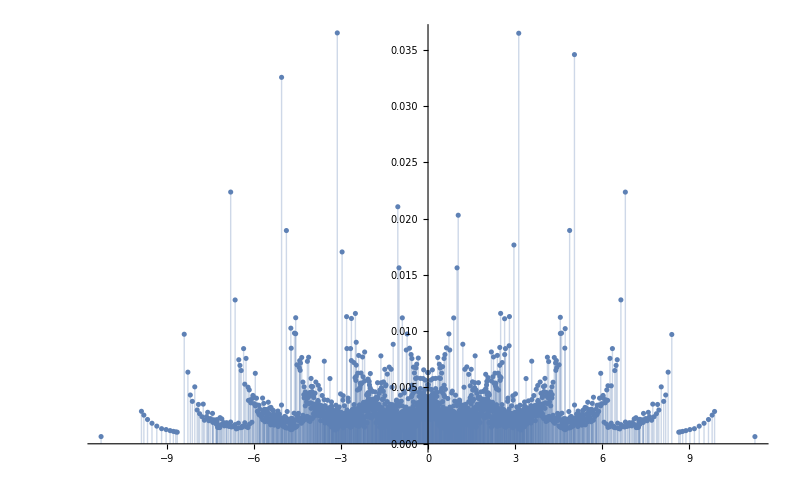
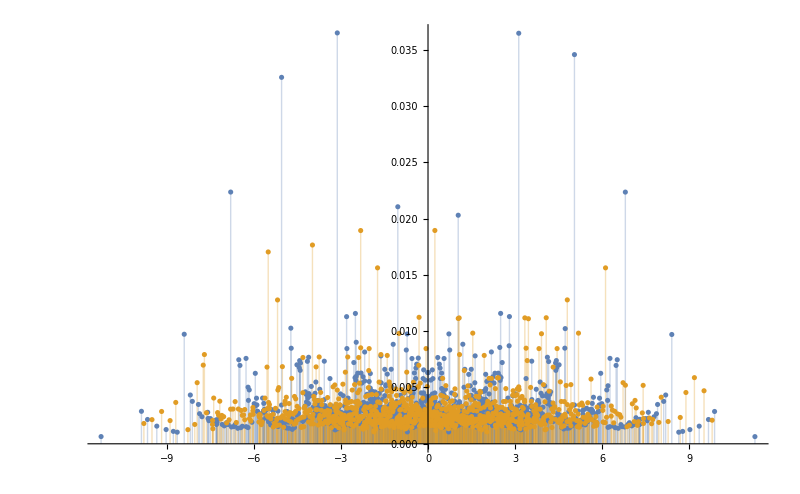

```mathematica
{ListPlot[Transpose[{eigVals,iprs}],PlotRange->All,Filling->Axis,ImageSize->800],ListPlot[{Transpose[{EvenEigVals,iprsEven}],Transpose[{OddEigVals,iprsOdd}]},PlotRange->All,Filling->Axis,ImageSize->800]}
```

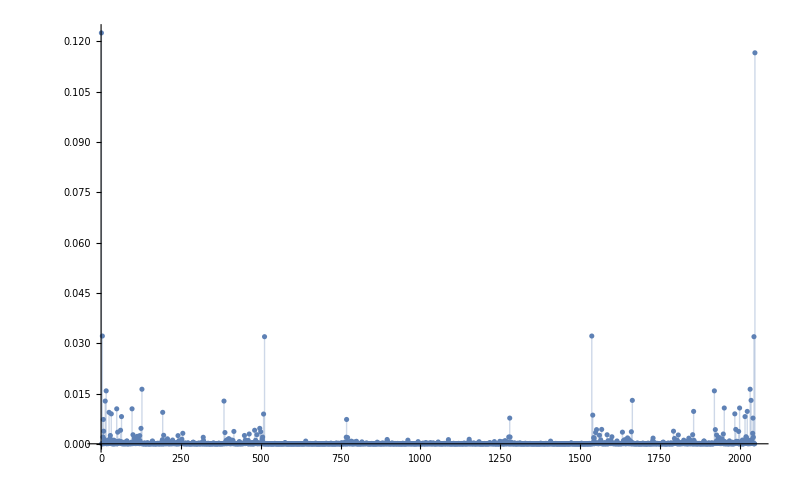
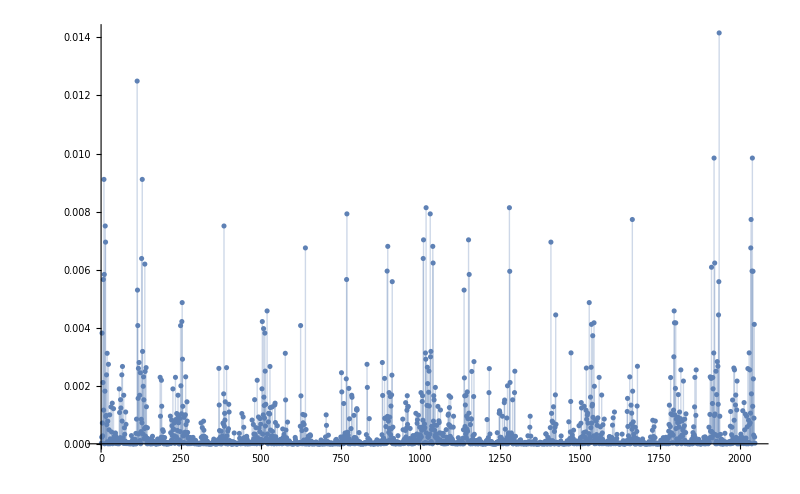

```mathematica
{ListPlot[Abs[eigVecs[[390]]]^2,PlotRange->All,Filling->Axis,ImageSize->800],ListPlot[Abs[eigVecs[[88]]]^2,PlotRange->All,Filling->Axis,ImageSize->800]}
```

```mathematica
DuplicateFreeQ[EvenEigVals]
```

True

```mathematica
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
```

{0.298113,0.264786}

```mathematica
Length[EvenEigVals]
```

952

```mathematica
Length[OddEigVals]
```

894

### To compute the whole diagram

```mathematica
missingValues=Complement[Round[Flatten[Table[{i,j},{i,0.01,3,0.01},{j,0.01,3,0.01}],1],10.^-2],Round[MeanLevelSpacingRatioData[[2;;,{1,2}]],10.^-3]]
```

```mathematica
(*Parece que tarda 2.05~2.1 s por iteración, debería tardar approx 41 min*)
AbsoluteTiming[
Do[
Module[
{H,eigVals,eigVecs,EvenEigVals,hz,J},
{hz,J}=hzJ;
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
EvenEigVals=eigVals[[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]]];
AppendTo[MeanLevelSpacingRatioData,{hz,J,MeanLevelSpacingRatio[EvenEigVals]}];
],{hzJ,missingValues}
]
]
```

{28125.8,Null}

#### Nueva versión, 22 Mar 2025

```mathematica
points = Tuples[Join[Flatten[Table[Subdivide[#[[i]],#[[i+1]],3][[1;;3]],{i,9}]],{2.95}],2]&[Subdivide[0.05,2.95,9]];
```

```mathematica
L=11(*número de espines*);

newIndices=FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L](*indices*);
eigenvals={};

AbsoluteTiming[
Do[
{hz,J}=i;

(* Construir Hamiltoniano y diagonalizarlo *)
H=IsingNNOpenHamiltonian[(*hx*)1.,hz,J,(*L*)11];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];

(* Encontrar la posición de los eigenvectores pares *)
eigenvecsParities=Round[Map[Braket[#,#[[newIndices]]]&,eigVecs],10.^0];
evenEigenvecsPositions=Flatten[Position[eigenvecsParities,1.]];
EvenEigVals=eigVals[[evenEigenvecsPositions]];
AppendTo[eigenvals,EvenEigVals]
,{i,points}];
]
```

{911.377,Null}

```mathematica
Export["~/Documents/chaos_meets_channels/ja_files/data/energies/wisniacki_open/L_11/hx_1_hz_J_0.05-2.95.csv",eigenvals,"CSV"]
```

~/Documents/chaos_meets_channels/ja_files/data/energies/wisniacki_open/L_11/hx_1_hz_J_0.05-2.95.csv

```mathematica
eigenvals=ToExpression[Import["~/data_backup/energies/wisniacki_open/L_11/hx_1_hz_J_0.05-2.95.csv","CSV"]];
```

```mathematica
eigenvals[[1]]
```

{-11.0213,-9.11446,-9.08778,-9.04222,-8.99064,-8.9468,-8.92182,-7.19729,-7.17063,-7.15983,-7.13316,-7.12512,-7.10955,-7.08762,-7.08285,-7.07357,-7.06025,-7.03729,-7.03605,-7.03355,-7.02976,-7.02475,-7.00479,-6.99804,-6.99223,-6.98796,-6.9857,-6.96726,-6.95245,-6.94186,-6.93635,-6.91689,-6.90082,-6.89249,-6.8675,-6.85695,-6.83195,-5.26383,-5.22639,-5.21836,-5.1917,-5.1809,-5.17614,-5.16686,-5.15423,-5.14468,-5.14018,-5.13062,-5.12938,-5.12687,-5.12308,-5.10393,-5.10269,-5.09823,-5.09644,-5.0954,-5.09465,-5.09138,-5.08559,-5.08133,-5.07908,-5.07144,-5.06076,-5.05994,-5.05891,-5.05714,-5.05463,-5.05237,-5.05085,-5.04584,-5.04507,-5.03527,-5.03393,-5.02976,-5.02589,-5.01913,-5.01332,-5.01043,-5.00961,-5.00858,-5.00755,-5.0068,-5.00305,-4.99927,-4.99426,-4.98836,-4.98594,-4.98359,-4.9743,-4.97203,-4.96753,-4.96296,-4.96172,-4.96109,-4.96027,-4.95924,-4.95746,-4.95042,-4.93799,-4.93675,-4.93424,-4.93045,-4.92553,-4.92372,-4.92269,-4.92193,-4.9136,-4.91134,-4.8987,-4.89289,-4.88862,-4.88636,-4.87806,-4.87228,-4.86196,-4.85307,-4.84248,-4.83696,-4.8264,-4.8014,-4.79307,-4.75749,-3.30933,-3.26388,-3.25912,-3.23723,-3.22167,-3.21364,-3.21239,-3.20988,-3.18697,-3.18573,-3.17617,-3.17448,-3.17243,-3.17168,-3.16863,-3.16438,-3.16213,-3.14949,-3.14378,-3.14199,-3.14021,-3.1377,-3.13694,-3.13545,-3.12898,-3.12793,-3.12691,-3.12464,-3.12213,-3.11835,-3.11701,-3.11285,-3.10307,-3.10226,-3.10022,-3.09795,-3.09642,-3.09349,-3.09169,-3.09141,-3.09066,-3.08991,-3.08665,-3.08616,-3.08085,-3.07744,-3.07659,-3.07639,-3.07536,-3.07147,-3.06905,-3.06671,-3.06471,-3.05601,-3.0552,-3.05417,-3.05239,-3.05151,-3.0507,-3.04988,-3.04866,-3.0461,-3.04486,-3.04419,-3.04239,-3.04109,-3.0406,-3.03985,-3.03734,-3.03362,-3.03155,-3.0308,-3.02919,-3.02502,-3.02114,-3.0199,-3.01739,-3.01438,-3.01314,-3.00877,-3.00857,-3.00773,-3.00693,-3.00671,-3.00596,-3.00589,-3.00514,-3.00486,-3.00411,-3.00308,-2.9983,-2.99677,-2.99603,-2.99452,-2.99177,-2.98951,-2.98361,-2.98194,-2.98119,-2.97987,-2.97912,-2.97607,-2.97181,-2.97115,-2.96955,-2.96934,-2.96755,-2.96504,-2.96278,-2.96211,-2.9613,-2.95924,-2.95697,-2.95634,-2.95552,-2.95448,-2.9527,-2.94567,-2.94517,-2.94433,-2.94016,-2.93636,-2.9353,-2.93427,-2.932,-2.92949,-2.9257,-2.9237,-2.92078,-2.92019,-2.91897,-2.91793,-2.91717,-2.91342,-2.91049,-2.90968,-2.90884,-2.90762,-2.89872,-2.8963,-2.89395,-2.88813,-2.88473,-2.88386,-2.88367,-2.88263,-2.87633,-2.8733,-2.87206,-2.8714,-2.86959,-2.86779,-2.8572,-2.84831,-2.84707,-2.84456,-2.84084,-2.83876,-2.838,-2.83221,-2.82391,-2.82164,-2.80318,-2.79891,-2.79664,-2.78831,-2.77223,-2.75273,-2.74721,-2.70328,-1.33057,-1.28036,-1.27911,-1.24292,-1.23541,-1.23364,-1.23112,-1.22887,-1.21052,-1.20698,-1.19573,-1.19368,-1.19141,-1.18988,-1.18516,-1.18413,-1.18338,-1.17962,-1.16503,-1.16324,-1.16026,-1.1582,-1.15746,-1.15671,-1.14872,-1.14767,-1.1459,-1.14422,-1.14339,-1.14216,-1.1396,-1.13836,-1.13826,-1.13589,-1.13411,-1.12281,-1.122,-1.11921,-1.11475,-1.1135,-1.11295,-1.11192,-1.1117,-1.11098,-1.10791,-1.10742,-1.10666,-1.1021,-1.10048,-1.09945,-1.0987,-1.0984,-1.09765,-1.09662,-1.09184,-1.09031,-1.08806,-1.08797,-1.08672,-1.07727,-1.07646,-1.07557,-1.07543,-1.07353,-1.07278,-1.07272,-1.07197,-1.06992,-1.0697,-1.06612,-1.06545,-1.06365,-1.0632,-1.0629,-1.06139,-1.06112,-1.06036,-1.0586,-1.05635,-1.05489,-1.05281,-1.05054,-1.05045,-1.04912,-1.04807,-1.04629,-1.04296,-1.04117,-1.03875,-1.03866,-1.03799,-1.0364,-1.03441,-1.03004,-1.02899,-1.02819,-1.02797,-1.02716,-1.02613,-1.0257,-1.02489,-1.02385,-1.02319,-1.02237,-1.01957,-1.01938,-1.0173,-1.01655,-1.01579,-1.01388,-1.01258,-1.01207,-1.01154,-1.01078,-1.00703,-1.00331,-1.00322,-1.00246,-1.00123,-1.00114,-0.99887,-0.997341,-0.992621,-0.992421,-0.991582,-0.990826,-0.99061,-0.98765,-0.98707,-0.984816,-0.984059,-0.981864,-0.981052,-0.978449,-0.978247,-0.977607,-0.977404,-0.976793,-0.9766,-0.976377,-0.97576,-0.975565,-0.974534,-0.970038,-0.966947,-0.966449,-0.965702,-0.965609,-0.963234,-0.961442,-0.95612,-0.955061,-0.953278,-0.951616,-0.950856,-0.950766,-0.94954,-0.946981,-0.945737,-0.943271,-0.942061,-0.941477,-0.940816,-0.940246,-0.939211,-0.939001,-0.938299,-0.934704,-0.934585,-0.932528,-0.931776,-0.931718,-0.930961,-0.928903,-0.925992,-0.925178,-0.924144,-0.917586,-0.915329,-0.915236,-0.913991,-0.909418,-0.907812,-0.906773,-0.90602,-0.905716,-0.904963,-0.903925,-0.89914,-0.897614,-0.89695,-0.895354,-0.893354,-0.892691,-0.890873,-0.890432,-0.888616,-0.887578,-0.882123,-0.881311,-0.878496,-0.870166,-0.86837,-0.865948,-0.865854,-0.863594,-0.862135,-0.860051,-0.857774,-0.856356,-0.855297,-0.853506,-0.84655,-0.845966,-0.843703,-0.842947,-0.84104,-0.839224,-0.82448,-0.819754,-0.818709,-0.817951,-0.814192,-0.810471,-0.809613,-0.808387,-0.797138,-0.793536,-0.774045,-0.7728,-0.770331,-0.76853,-0.757927,-0.724605,-0.722342,-0.672881,0.673964,0.723167,0.725433,0.758573,0.76914,0.77091,0.773429,0.774654,0.794031,0.797573,0.808823,0.810071,0.810875,0.81468,0.818374,0.819123,0.820155,0.824938,0.839531,0.841322,0.843272,0.844022,0.846365,0.84683,0.8538,0.85557,0.856617,0.858096,0.860344,0.862404,0.863936,0.866207,0.866298,0.868675,0.870459,0.878703,0.881489,0.882294,0.887763,0.888796,0.89059,0.891065,0.892863,0.893582,0.895631,0.897147,0.897905,0.899375,0.904085,0.905119,0.905866,0.906167,0.906917,0.907945,0.909636,0.914257,0.915482,0.915574,0.917847,0.924222,0.925264,0.92606,0.928997,0.931044,0.931797,0.931852,0.932603,0.934643,0.93487,0.938446,0.939125,0.939316,0.94035,0.940926,0.941669,0.942149,0.943452,0.945967,0.947191,0.949684,0.950933,0.951026,0.951758,0.953397,0.955178,0.956231,0.961616,0.963403,0.965826,0.965918,0.966586,0.967142,0.970166,0.974541,0.975585,0.975789,0.976384,0.97661,0.976834,0.977419,0.977633,0.978317,0.978446,0.981118,0.981927,0.984167,0.984924,0.987279,0.987754,0.990703,0.990968,0.991723,0.992506,0.992761,0.997549,0.999014,1.00127,1.00136,1.00261,1.00334,1.00343,1.00724,1.01092,1.01168,1.01216,1.01272,1.01397,1.01589,1.01665,1.01751,1.01949,1.01964,1.02244,1.02325,1.02388,1.02493,1.02573,1.02613,1.02718,1.02798,1.0282,1.02902,1.03004,1.03454,1.0366,1.03813,1.03888,1.03897,1.04134,1.04314,1.0464,1.04819,1.04924,1.05062,1.05071,1.05296,1.05504,1.05656,1.05884,1.06045,1.06131,1.06149,1.06311,1.0633,1.06377,1.06558,1.06628,1.06988,1.06999,1.07205,1.07281,1.07287,1.07362,1.07549,1.07568,1.07654,1.07734,1.087,1.08822,1.08831,1.09059,1.09205,1.09677,1.09781,1.09856,1.09887,1.09962,1.10066,1.10233,1.10697,1.10763,1.10819,1.11123,1.11189,1.11208,1.11312,1.11371,1.11493,1.11937,1.12219,1.123,1.13442,1.13622,1.13864,1.13873,1.13995,1.14245,1.1437,1.14453,1.14616,1.14795,1.14901,1.157,1.15776,1.15862,1.1606,1.16355,1.16536,1.18011,1.1838,1.18456,1.1856,1.19039,1.19186,1.19411,1.1962,1.20745,1.21105,1.22951,1.23179,1.23426,1.23606,1.24354,1.27998,1.28121,1.33171,2.70401,2.74773,2.75323,2.77262,2.78865,2.79696,2.79923,2.80351,2.82186,2.82413,2.83238,2.83817,2.83892,2.84097,2.84478,2.84726,2.84848,2.85729,2.86786,2.86964,2.87143,2.87216,2.87338,2.87647,2.88266,2.8837,2.88392,2.88474,2.88821,2.89405,2.89641,2.8988,2.90757,2.90882,2.90962,2.91042,2.91345,2.91713,2.91788,2.91892,2.92024,2.92071,2.92371,2.92576,2.9295,2.93197,2.93422,2.93525,2.9363,2.94019,2.94439,2.94516,2.9457,2.95258,2.95436,2.9554,2.9562,2.95689,2.95914,2.96119,2.96199,2.96274,2.96501,2.96748,2.96926,2.96954,2.97106,2.97181,2.97611,2.97907,2.97983,2.98117,2.9819,2.98354,2.98949,2.99177,2.99446,2.99606,2.99674,2.9982,3.00291,3.00394,3.00469,3.00498,3.00574,3.00578,3.00653,3.00676,3.00757,3.00847,3.00859,3.0131,3.01432,3.01743,3.0199,3.02113,3.02496,3.02917,3.03076,3.03152,3.03359,3.03739,3.03987,3.04053,3.04109,3.04232,3.04413,3.04484,3.04606,3.04855,3.0498,3.05061,3.05142,3.05226,3.05404,3.05509,3.05589,3.06471,3.06676,3.06914,3.07152,3.07532,3.07636,3.07657,3.07742,3.08088,3.08618,3.08673,3.08987,3.09062,3.09149,3.09166,3.09348,3.09646,3.09792,3.10017,3.10224,3.10304,3.11296,3.11717,3.11849,3.12223,3.12471,3.12696,3.128,3.12905,3.13554,3.13715,3.13782,3.14029,3.14208,3.14389,3.14957,3.16233,3.16462,3.16892,3.17188,3.17264,3.17472,3.17636,3.18598,3.1872,3.21031,3.21278,3.21401,3.22206,3.23766,3.25972,3.26447,3.3102,4.75762,4.79304,4.80135,4.82625,4.83678,4.8423,4.85288,4.86169,4.87199,4.87779,4.88605,4.88832,4.89261,4.89845,4.91096,4.91323,4.92154,4.92229,4.92333,4.92512,4.93016,4.93391,4.93638,4.9376,4.95011,4.957,4.95877,4.95981,4.9606,4.9613,4.96252,4.96715,4.97162,4.97395,4.98321,4.98558,4.98796,4.9939,4.99888,5.00262,5.0063,5.00705,5.00808,5.00913,5.00992,5.01289,5.01874,5.02554,5.02938,5.03359,5.0349,5.04467,5.04551,5.05048,5.05194,5.05422,5.05668,5.05847,5.05951,5.0603,5.07118,5.07871,5.081,5.0853,5.09115,5.09429,5.09505,5.09609,5.09789,5.10234,5.10357,5.12291,5.12666,5.12913,5.13035,5.13996,5.14443,5.15399,5.16676,5.17603,5.18079,5.19163,5.21843,5.22648,5.26414,6.83129,6.8562,6.86673,6.89165,6.89996,6.91601,6.93541,6.94093,6.95153,6.96636,6.98471,6.98699,6.99129,6.99714,7.00393,7.02389,7.02887,7.03262,7.03509,7.03631,7.05938,7.07269,7.08195,7.0867,7.10873,7.12432,7.13237,7.15916,7.17,7.19679,8.92026,8.94519,8.98897,9.04057,9.08622,9.113,11.0188}

```mathematica
rTilde=MeanLevelSpacingRatio/@eigenvals;
rTilde=Table[Join[points[[i]],{rTilde[[i]]}],{i,784}];
```

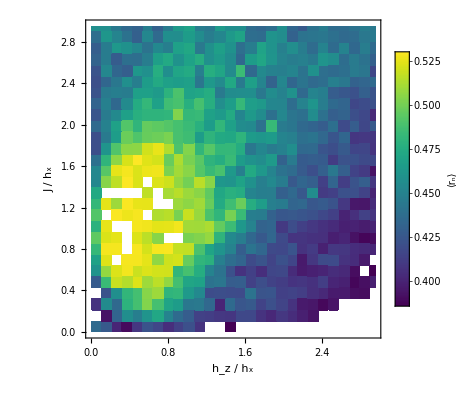

```mathematica
fontSize=18;
fig=
ListDensityPlot[rTilde,
PlotRange->{0.386,0.531},
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
rTilde=MeanLevelSpacingRatio/@eigenvals;rTilde=If[#<0.386,0.386,If[#>0.531,0.531,#]]&/@rTilde;
rTilde=Table[Join[points[[i]],{rTilde[[i]]}],{i,784}];
```

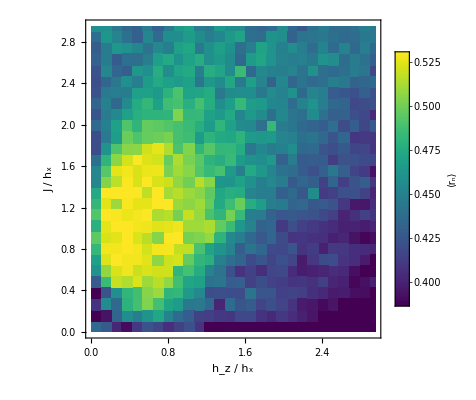

```mathematica
fontSize=18;
fig=
ListDensityPlot[rTilde,
PlotRange->{0.386,0.531},
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
rTilde=MeanLevelSpacingRatio/@eigenvals;rTilde=Rescale[rTilde,MinMax[rTilde],{0.386,0.531}];
rTilde=Table[Join[points[[i]],{rTilde[[i]]}],{i,784}];
```

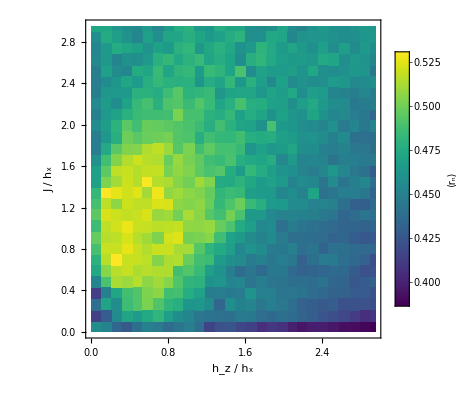

```mathematica
fontSize=18;
fig=
ListDensityPlot[rTilde,
PlotRange->{0.386,0.531},
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
Select[points,Round[#[[2]],10.^-1]==1.4&]
```

{{0.05,1.4463},{0.157407,1.4463},{0.264815,1.4463},{0.372222,1.4463},{0.47963,1.4463},{0.587037,1.4463},{0.694444,1.4463},{0.801852,1.4463},{0.909259,1.4463},{1.01667,1.4463},{1.12407,1.4463},{1.23148,1.4463},{1.33889,1.4463},{1.4463,1.4463},{1.5537,1.4463},{1.66111,1.4463},{1.76852,1.4463},{1.87593,1.4463},{1.98333,1.4463},{2.09074,1.4463},{2.19815,1.4463},{2.30556,1.4463},{2.41296,1.4463},{2.52037,1.4463},{2.62778,1.4463},{2.73519,1.4463},{2.84259,1.4463},{2.95,1.4463}}

```mathematica
Position[Round[points,10.^-2],x_/;x=={0.48,1.45}]
```

{{126}}

```mathematica
points[[120]]
```

{0.47963,0.801852}

```mathematica
Position[MeanLevelSpacingRatio[eigenvals[[#,IntegerPart[1056*x];;IntegerPart[1056*(1-x)]]]]&/@Range[784],x_/;Round[x,10.^-2]==0.43]
```

{{1},{21},{25},{27},{51},{58},{59},{80},{108},{112},{140},{195},{196},{254},{369},{371},{395},{397},{399},{400},{417},{423},{429},{444},{452},{456},{457},{458},{475},{476},{480},{485},{486},{487},{499},{504},{515},{517},{520},{544},{545},{546},{547},{555},{559},{560},{572},{574},{576},{582},{602},{604},{607},{611},{628},{631},{635},{640},{664},{666},{687},{689},{690},{694},{699},{716},{719},{723},{742},{750},{751},{775},{778},{781}}

```mathematica
(MeanLevelSpacingRatio[eigenvals[[#,IntegerPart[1056*x];;IntegerPart[1056*(1-x)]]]]&/@Range[784])[[140]]
```

0.434908

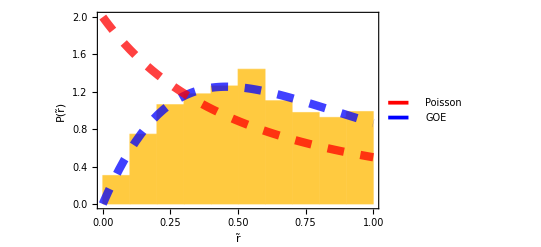

```mathematica
x=0.05;
r=Ratios[Differences[eigenvals[[120,IntegerPart[1056*x];;IntegerPart[1056*(1-x)]]]]];
rTilde=Min/@Transpose[{r,1/r}];PlotPr[rTilde]
```

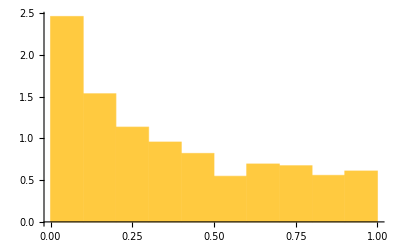

```mathematica
Histogram[rTilde,Automatic,"PDF"]
```

```mathematica
Eigenvalues[IsingNNOpenHamiltonian[1.,1.66,0.,2]]
```

{3.87587,-3.87587,-6.88685×10^-16,0.}

```mathematica
Eigenvalues[IsingNNOpenHamiltonian[1.,1.66,0.01,2]]
```

{-3.88322,3.86855,0.01,0.00467454}

```mathematica
L=4;
newIndices=FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L](*indices*);

(* Construir Hamiltoniano y diagonalizarlo *)
H=IsingNNOpenHamiltonian[1.,1.66,0.,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];

(* Encontrar la posición de los eigenvectores pares *)
eigenvecsParities=Round[Map[Braket[#,#[[newIndices]]]&,eigVecs],10.^0];
evenEigenvecsPositions=Flatten[Position[eigenvecsParities,1.]];
EvenEigVals=Chop[eigVals[[evenEigenvecsPositions]]]

(* Construir Hamiltoniano y diagonalizarlo *)
H=IsingNNOpenHamiltonian[1.,1.66,0.05,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];

(* Encontrar la posición de los eigenvectores pares *)
eigenvecsParities=Round[Map[Braket[#,#[[newIndices]]]&,eigVecs],10.^0];
evenEigenvecsPositions=Flatten[Position[eigenvecsParities,1.]];
EvenEigVals=Chop[eigVals[[evenEigenvecsPositions]]]
```

{-7.75175,-3.87587,0,0,3.87587,7.75175}

{-7.8631,-3.91577,-3.84912,-0.0379603,0.0282627,0.0366975,0.119693,3.83679,3.90145,7.64306}

### Aquí sigue lo viejo

```mathematica
MeanLevelSpacingRatioData[[1]]
```

{h_z/h_x,J/h_x,<r_n>}

```mathematica
{info,MeanLevelSpacingRatioData}={#[[1;;2]],#[[3;;]]}&[Import["data/mean_level_spacing_ratio/wisniacki_open_L_11_hx_1.csv","CSV"]];
info
```

{{# Wisniacki open chain, L=11, hx=1},{h_z/h_x,J/h_x,<r_n>}}

Tenemos 90,000 puntos:

```mathematica
MeanLevelSpacingRatioData//Dimensions
```

{90000,3}

```mathematica
fontSize=18;
fig=
ListDensityPlot[MeanLevelSpacingRatioData[[3;;]](*para excluir el primer elemento {hz/hx, J/hx, <r_n>}*),
PlotRange->{0.38,0.53},
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

-Graphics-

```mathematica
fontSize=18;
fig=
ListDensityPlot[MeanLevelSpacingRatioData[[3;;]](*para excluir el primer elemento {hz/hx, J/hx, <r_n>}*),
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

-Graphics-

#### Arreglando datos (cambiar nombre)

```mathematica
{info,MeanLevelSpacingRatioData}={#[[1;;2]],ToExpression[#[[3;;]]]}&[Import["data/mean_level_spacing_ratio/wisniacki_open_L_11_hx_1.csv","CSV"]];
info
MeanLevelSpacingRatioData=If[#[[3]]<0.386,{#[[1]],#[[2]],0.386},If[#[[3]]>0.531,{#[[1]],#[[2]],0.531},#]]&/@MeanLevelSpacingRatioData;
```

{{# Wisniacki open chain, L=11, hx=1},{h_z/h_x,J/h_x,<r_n>}}

```mathematica
MeanLevelSpacingRatioData[[1]]
```

{0.05,0.05,0.435876}

```mathematica
fontSize=18;
fig=
ListDensityPlot[MeanLevelSpacingRatioData,
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

-Graphics-

```mathematica
(*Define the input and output file paths*)
filename="figs_ja/mean_level_spacing_ratio/wisniacki_open_L_7_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/mean_level_spacing_ratio/wisniacki_open_L_7_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/mean_level_spacing_ratio/wisniacki_open_L_7_hx_1.pdf'.
,StandardError→|>

## Export data and figure

```mathematica
(*Data*)
Export["/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/mean_level_spacing_ratio.csv",MeanLevelSpacingRatioData,"CSV"]
```

/home/jadeleon/Documents/quantum_chaotic_channels/numerica_JA/mean_level_spacing_ratio.csv

```mathematica
(*Figure*)
Export["/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png",fig,"PNG",ImageResolution->300]
```

/home/jadeleon/Documents/quantum_chaotic_channels/mean_level_spacing_ratio.png

## XXZ

```mathematica
ϵJxy=Tuples[Subdivide[0.05,4.96,29],2];
```

```mathematica
r=Flatten[Import["~/Documents/chaos_meets_channels/ja_files/data/mean_level_spacing_ratio/rs_mat_L_12_px_30_XXZ.csv","Table"]];
r=Table[Join[Reverse[ϵJxy[[i]]],{r[[i]]}],{i,900}];
r=If[#[[3]]<0.386,{#[[1]],#[[2]],0.386},If[#[[3]]>0.531,{#[[1]],#[[2]],0.531},#]]&/@r;
```

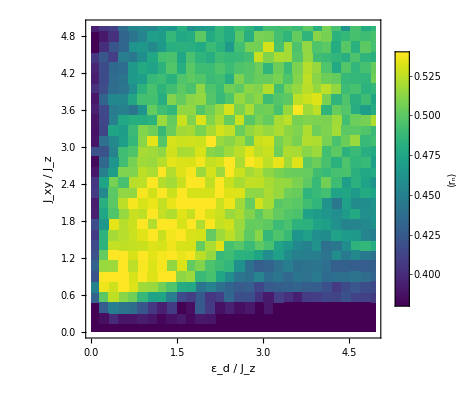

```mathematica
fontSize=18;
fig=
ListDensityPlot[r,
PlotRange->{0.38,0.531},
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[{Automatic,{0.38,0.54}},LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontSize->fontSize,Black],LegendMarkerSize->270],Automatic],
Frame->True,
FrameStyle->Directive[FontSize->fontSize,Black],
FrameLabel->{"ε_d / J_z","J_xy / J_z"},
AspectRatio->1
]
```

```mathematica
filename="~/Documents/chaos_meets_channels/ja_files/figs_ja/mean_level_spacing_ratio/xxz.pdf";
Export[filename,fig,"PDF",ImageResolution->300];RunProcess[{"pdfcrop",filename,filename}];
```

## Heisenberg con ruido

```mathematica
hz=Subdivide[0.05,4.96,29];
```

```mathematica
r=Flatten[Import["~/Documents/chaos_meets_channels/ja_files/data/mean_level_spacing_ratio/rs_mat_L_12_px_30_Heis.csv","Table"]];
r=Table[{hz[[i]],r[[i]]},{i,30}];
r=If[#[[2]]<0.386,{#[[1]],0.386},If[#[[2]]>0.531,{#[[1]],0.531},#]]&/@r;
```

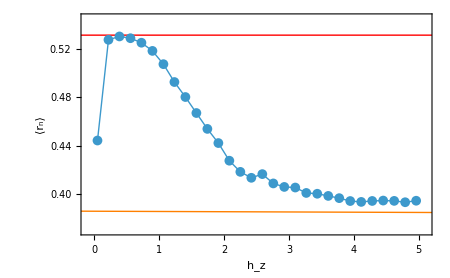

```mathematica
fig=ListPlot[r,
PlotRange->{{-0.1,5.1},{0.37,0.545}},
Joined->True,
PlotStyle->Directive[Thin],
PlotMarkers->{Automatic,10},
Frame->True,
FrameStyle->Directive[Black,Thick,FontSize->20],
FrameLabel->{"h_z","⟨r_n⟩"},
Epilog->{{Orange,InfiniteLine[{{0,0.386},{5,0.385}}]},{Red,InfiniteLine[{{0,0.531},{5,0.531}}]}},
ImageSize->450
]
```

```mathematica
filename="~/Documents/chaos_meets_channels/ja_files/figs_ja/mean_level_spacing_ratio/heisenberg.pdf";
Export[filename,fig,"PDF",ImageResolution->300];RunProcess[{"pdfcrop",filename,filename}];
```

## No secciones

## Mean level spacing ratio (r_n)(h_z/h_x,J/h_x) no se que es

```mathematica
L=11;{hx,hz,J}={1,0.5,1.};
(*se iba a tardar 20+ min*)
AbsoluteTiming[
Module[{H,eveneigenvecs,oddeigenvecs},
H=IsingNNOpenHamiltonian[hx,hz,ConstantArray[J,L-1],L];
{eveneigenvecs,oddeigenvecs}=ParityEigenvectors[L];
(*Even symmetric Hamiltonian*)
(*Heven=ParallelTable[Braket[a,b],{a,eveneigenvecs},{b,H.#&/@eveneigenvecs}];*)
c=H.#&/@eveneigenvecs;
Heven=Table[Braket[a,#]&/@c,{a,eveneigenvecs}];
]
]
```

{279.056,Null}

```mathematica
Sort[#]==#&[Eigenvalues[Heven]]
```

False

```mathematica
MeanLevelSpacingRatio[Sort[Eigenvalues[Heven]]]
```

0.520833

```mathematica
0.25*1056/60
```

4.4

## Wisniacki open, L=7, paridad +1

```mathematica
?MeanLevelSpacingRatio
```

```mathematica
{#[[1]],energies=#[[2;;,3;;]];}&[Import["data/energies/wisniacki_open/L_7/parity_plus1_hz_and_J_from_0_to_2_step_0.1.csv"]]
```

{{hz,J,E0,...,En, con n la dimension del subespacio},Null}

```mathematica
energies[[1]]
```

{-7.,-5.,-5.,-5.,-5.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-3.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,5.,5.,5.,5.,7.}

```mathematica
meanR=If[Head[#]===Real,#,0.]&/@(MeanLevelSpacingRatio/@energies[[;;,8;;-8]]);
```

Divide::indet: Indeterminate expression 0./0. encountered.

Divide::infy: Infinite expression (4.44089×10^-16)/0. encountered.

Divide::infy: Infinite expression (8.88178×10^-16)/0. encountered.

Divide::infy: Infinite expression (1.33227×10^-15)/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

```mathematica
meanR=Flatten[Table[{Subdivide[0.,2.,20][[i]],Subdivide[0.,2.,20][[j]],meanR[[21*(i-1)+j]]},{i,21},{j,21}],1];
```

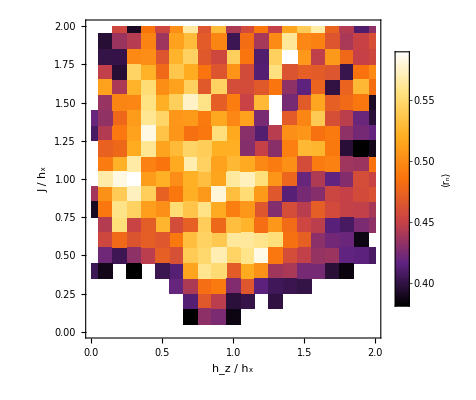

```mathematica
fontSize=22;

fig=ListDensityPlot[meanR,
ColorFunction->"SunsetColors",ColorFunctionScaling->True,
PlotRange->{0.38,0.6},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}
]
```

```mathematica
Export["figs_ja/tmp/mean_level_spacing_ratio_wisniacki_open_L_7.png",fig,"PNG"]
```

figs_ja/tmp/mean_level_spacing_ratio_wisniacki_open_L_7.png